### Linear Stability Analysis of Halo Problem

Halo Problem

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/halo

#### Single Beam Eigensystem

```mathematica
egs[omegav_,refl_,xi_,mu_]:= {
{-omegav+refl*xi*mu,-refl*xi*mu},
{xi*mu,omegav-xi*mu}
}
```

```mathematica
egssol[omegav_,refl_,xi_,mu_]:=Eigensystem[egs[omegav,refl,xi,mu]]//FullSimplify
```

```mathematica
amp[omegav_,refl_,xi_,mu_,idx_,iniCon_,z_:0]:=Module[{reflM,muM,xiM,omegavM,egvM,evalM,cpM,cmM},

omegavM=omegav;
reflM=refl;
xiM=xi;
muM=mu;

egvM=egssol[omegavM,reflM,xiM,muM][[2]];
evalM=egssol[omegavM,reflM,xiM,muM][[1]];

cpM=(iniCon[[1]]-iniCon[[2]]egvM[[2,1]])/(egvM[[1,1]]-egvM[[2,1]]);
cmM=iniCon[[2]]-cpM;

cpM*egvM[[1,idx]]Exp[-I evalM[[1]] z]+cmM*egvM[[2,idx]]Exp[-I evalM[[2]] z]

]
```

```mathematica
init={10^(-2),0.00522371+0.0433973I};
R=0.05;
muVal=1;
xiVal=2;
```

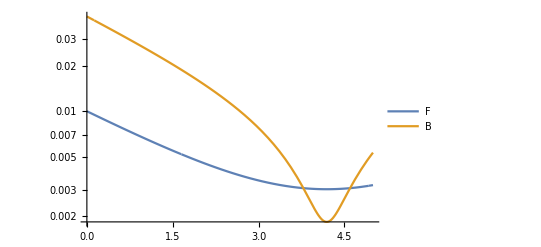

```mathematica
LogPlot[{Abs@amp[1,R,xiVal,muVal,1,init,z],Abs@amp[1,R,xiVal,muVal,2,init,z]},{z,0,5},PlotLegends->{"F","B"}]
```

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[0.01].

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[0.0426551].

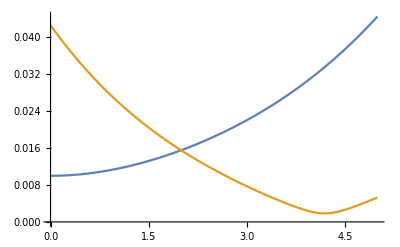

```mathematica
Plot[{First@Differences@Abs@amp[1,0.05,2,1.5,1,{10^(-2),10^(-2)},z],First@Differences@Abs@amp[1,0.05,2,1.0,2,{10^(-2),0.00522371+0.0433973I},z]},{z,0,5}]
```

#### Phase Portrait

```mathematica
Manipulate[
Grid[{{
VectorPlot[Re[-I egs[1,R,xiVal,muVal].{x+xIm I,y+yIm I}],{x,-0.1,0.1},{y,-0.1,0.1},FrameLabel->{"Re ϵ_F","Re ϵ_B"},PlotLabel->"Phase Portrait ( {Im ϵ_F,Im ϵ_B}="<>ToString@{xIm,yIm}<>")",StreamPoints->Coarse,PlotTheme->"Scientific",ImageSize->Medium,VectorStyle->White],
VectorPlot[Im[-I egs[1,R,xiVal,muVal].{x+xIm I,y+yIm I}],{x,-0.1,0.1},{y,-0.1,0.1},FrameLabel->{"Re ϵ_F","Re ϵ_B"},PlotLabel->"Phase Portrait ( {Im ϵ_F,Im ϵ_B}="<>ToString@{xIm,yIm}<>")",StreamPoints->Coarse,PlotTheme->"Scientific",ImageSize->Medium,VectorStyle->White]
},
{
VectorPlot[Re[-I egs[1,R,xiVal,muVal].{xRe+x I,yRe+y I}],{x,-0.1,0.1},{y,-0.1,0.1},FrameLabel->{"Im ϵ_F","Im ϵ_B"},PlotLabel->"Phase Portrait ( {Re ϵ_F,Re ϵ_B}="<>ToString@{xRe,yRe}<>")",StreamPoints->Coarse,PlotTheme->"Scientific",ImageSize->Medium,VectorStyle->White],
VectorPlot[Im[-I egs[1,R,xiVal,muVal].{xRe+x I,yRe+y I}],{x,-0.1,0.1},{y,-0.1,0.1},FrameLabel->{"Im ϵ_F","Im ϵ_B"},PlotLabel->"Phase Portrait ( {Re ϵ_F,Re ϵ_B}="<>ToString@{xRe,yRe}<>")",StreamPoints->Coarse,PlotTheme->"Scientific",ImageSize->Medium,VectorStyle->White]
}
}
],
{{xIm,0,"Imaginary Part of ϵ_F"},-0.1,0.1},
{{yIm,0,"Imaginary Part of ϵ_B"},-0.1,0.1},
{{xRe,0,"Real Part of ϵ_F"},-0.1,0.1},
{{yRe,0,"Reeal Part of ϵ_B"},-0.1,0.1}
]
```

### Solving from Reflection Point

```mathematica
Eigensystem@{
{-omegav+refl*xi*mu,-refl*xi*mu},
{xi*mu,omegav-xi*mu}
}//FullSimplify
```

{{1/2 (mu (-1+refl) xi-√(4 omegav^2-4 mu omegav (1+refl) xi+mu^2 (-1+refl)^2 xi^2)),1/2 (mu (-1+refl) xi+√(4 omegav^2-4 mu omegav (1+refl) xi+mu^2 (-1+refl)^2 xi^2))},{{-(2 omegav-mu (1+refl) xi+√(4 omegav^2-4 mu omegav (1+refl) xi+mu^2 (-1+refl)^2 xi^2))/(2 mu xi),1},{(-2 omegav+mu (1+refl) xi+√(4 omegav^2-4 mu omegav (1+refl) xi+mu^2 (-1+refl)^2 xi^2))/(2 mu xi),1}}}

```mathematica
solRefl[z_,end_,refl_,xi_,mu_,eta_,const_]:=Module[{vpM,vmM,omegavM,deltaM,omegapM,omegamM},

omegavM=eta;
deltaM=(1-refl)^2 mu^2 xi^2-4(1+refl)mu xi omegavM+4omegavM^2;

omegapM=((refl-1)mu xi + √deltaM)/2;
omegamM=((refl-1)mu xi - √deltaM)/2;

vmM={(-2omegavM+mu xi (1+refl)-√deltaM)/(2 xi mu),1};
vpM={(-2omegavM+mu xi (1+refl)+√deltaM)/(2 xi mu),1};

const*( ( √deltaM+mu xi (1-refl)+2omegavM )*vpM*Exp[-I omegapM (z-end) ] + (√deltaM-mu xi (1-refl)-2omegavM)*vmM*Exp[-I omegamM(z-end)] )

]
```

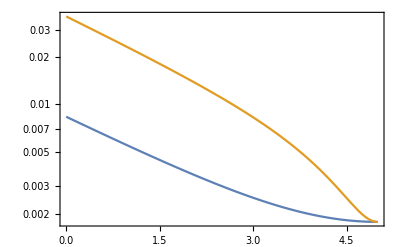

```mathematica
LogPlot[
Evaluate@Abs@solRefl[z,5,0.05,2,1,1,10^(-3)],
{z,0,5},Frame->True
]
```

### Why only Decreasing mode

The solution shows that we only get the decreasing mode. Why?

```mathematica
((I delta + a)(I delta + b)Exp[delta(z-L)]+(I delta -a)(-I delta +b)Exp[-delta(z-L)])*((-I delta + a)(-I delta + b)Exp[delta(z-L)]+(-I delta -a)(I delta +b)Exp[-delta(z-L)])//FullSimplify
```

2 (-a^2 b^2+(a^2+4 a b+b^2) delta^2-delta^4+(a^2+delta^2) (b^2+delta^2) Cosh[2 delta (L-z)])

```mathematica
((I delta + 2omegav + xi mu (1-R) )(I delta + mu xi (1+R) - 2omegav )Exp[delta(z-L)]+(I delta - 2omegav - xi mu (1-R) )(-I delta + mu xi (1+R) - 2omegav )Exp[-delta(z-L)])*((-I delta + 2omegav + xi mu (1-R) )(-I delta + mu xi (1+R) - 2omegav )Exp[delta(z-L)]+(-I delta - 2omegav - xi mu (1-R) )(I delta  + mu xi (1+R) - 2omegav )Exp[-delta(z-L)])//FullSimplify
```

16. delta^2 mu^2 xi^2 Cosh[delta (L-z)]^2+(4. delta^4+64. omegav^4-6.4 mu omegav^3 xi-31.76 mu^2 omegav^2 xi^2+1.596 mu^3 omegav xi^3+3.98002 mu^4 xi^4+delta^2 (32. omegav^2-1.6 mu omegav xi-7.98 mu^2 xi^2)) Sinh[delta (L-z)]^2

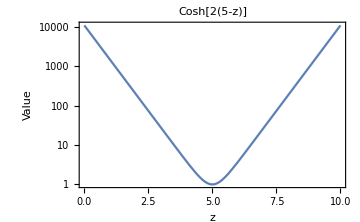

```mathematica
LogPlot[Cosh[2(5-z)],{z,0,10},Frame->True,ImageSize->Medium,FrameLabel->{"z","Value"},PlotLabel->"Cosh[2(5-z)]"]
```

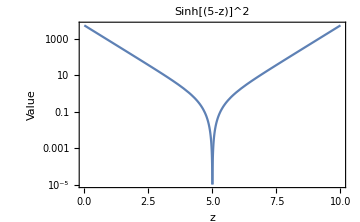

```mathematica
LogPlot[Sinh[(5-z)]^2,{z,0,10},Frame->True,ImageSize->Medium,FrameLabel->{"z","Value"},PlotLabel->"Sinh[(5-z)]^2"]
```

```mathematica
((I + 1)(I + 1)Exp[(z-5)]+(I -1)(-I  +1)Exp[-(z-5)])*((-I + 1)(-I + 1)Exp[(z-5)]+(-I -1)(I  +1)Exp[-(z-5)])//Simplify
```

4 ⅇ^(-2 (5+z)) (ⅇ^10+ⅇ^(2 z))^2

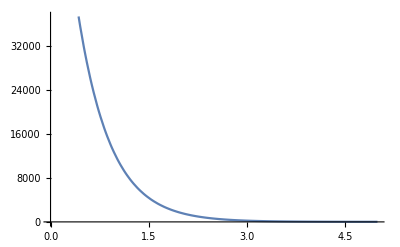

```mathematica
Plot[4 E^(-2 (5+z)) (E^10+E^(2 z))^2,{z,0,5}]
```

### Single Beam

```mathematica
(*
fp[r_,eta_]:=(-2(r+1)eta+8 √r)/(1-r)^2
fm[r_,eta_]:=(-2(r+1)eta-8 √r)/(1-r)^2
*)
xi=2;
fp[r_,eta_]:=(2(r+1)eta+4 √r)/(xi(1-r)^2)
fm[r_,eta_]:=(2(r+1)eta-4 √r)/(xi(1-r)^2)
```

```mathematica
Grid[
Transpose@Join[
{Join[
{""},
Table[r,{r,0.01,0.1,0.01}]
]},
Transpose[
Join[
{Table[eta,{eta,{-1,1}}]},
Table[{fm[r,eta],fp[r,eta]},{r,0.01,0.1,0.01},{eta,{-1,1}}]
]
]
],
Frame->All
]
```

| -1 | 1
0.01 | {-1.23457,-0.826446} | {0.826446,1.23457}
0.02 | {-1.35656,-0.767552} | {0.767552,1.35656}
0.03 | {-1.46287,-0.726528} | {0.726528,1.46287}
0.04 | {-1.5625,-0.694444} | {0.694444,1.5625}
0.05 | {-1.65896,-0.667907} | {0.667907,1.65896}
0.06 | {-1.75407,-0.645204} | {0.645204,1.75407}
0.07 | {-1.84894,-0.625332} | {0.625332,1.84894}
0.08 | {-1.94434,-0.60765} | {0.60765,1.94434}
0.09 | {-2.04082,-0.591716} | {0.591716,2.04082}
0.1 | {-2.13883,-0.577215} | {0.577215,2.13883}

Define a function that calculates the exponential growth

```mathematica
expGrow[refl_,xi_,mu_,eta_]=Im@√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta+4)/2;
solTheory[z_,refl_,xi_,mu_,eta_]=10^(-2){Exp[I((1-refl)xi mu/2-√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta+4)/2)z],Exp[I((1-refl)xi mu/2+√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta+4)/2)z]};

expGrow2[refl_,xi_,mu_,eta_]=Im@√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta/2+1)/2;
solTheory2[z_,refl_,xi_,mu_,eta_]=10^(-2){Exp[I((1-refl)xi mu/2-√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta/2+1)/2)z],Exp[I((1-refl)xi mu/2+√((1-refl)^2xi^2mu^2-4(1+refl)xi mu eta/2+1)/2)z]};
```

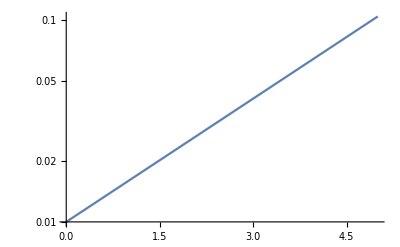

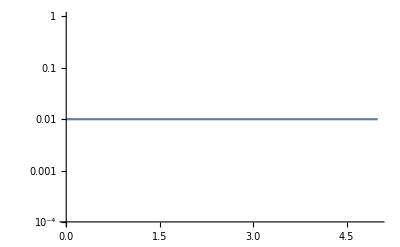

0.469468

0

```mathematica
LogPlot[Evaluate@Abs@solTheory[z,0.05,2,1.2,1][[1]],{z,0,5}]
LogPlot[Evaluate@Abs@solTheory2[z,0.05,2,1.2,1][[1]],{z,0,5}]
expGrow[0.05,2,1.2,1]
expGrow2[0.05,2,1.2,1]
```

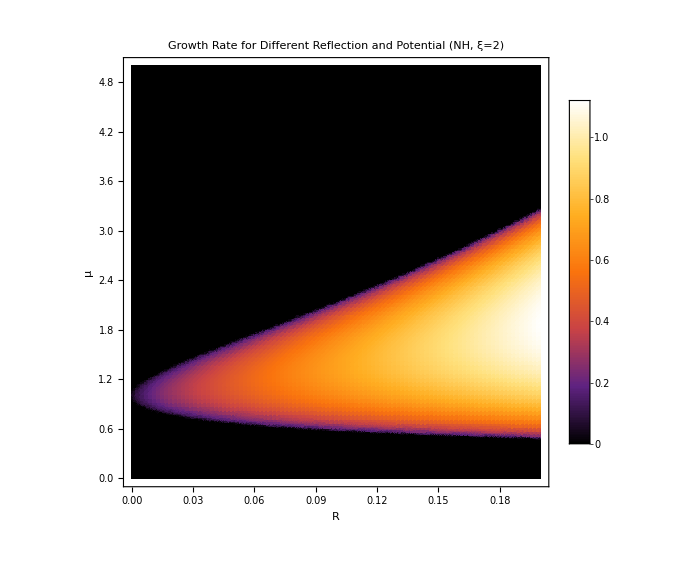

```mathematica
DensityPlot[expGrow[reflX,2,muX,1],{reflX,0.,0.2},{muX,0,5},FrameLabel->{"R","μ"},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->100,PlotLabel->"Growth Rate for Different Reflection and Potential (NH, ξ=2)",ImageSize->Large]
```

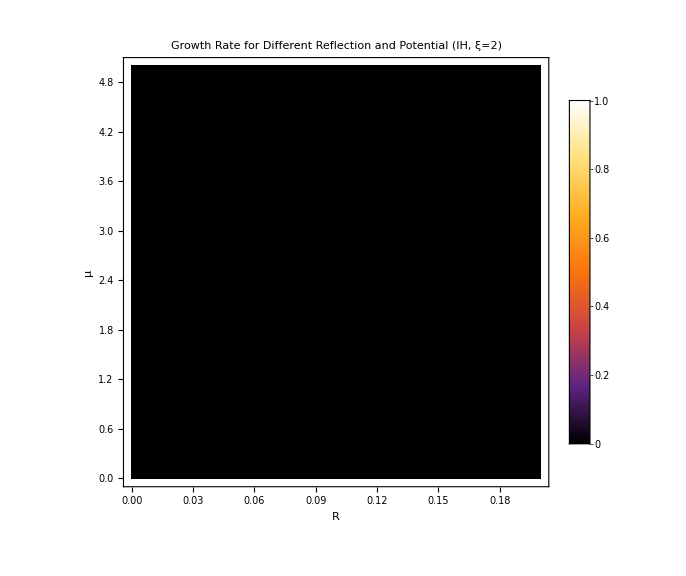

```mathematica
DensityPlot[expGrow[reflX,2,muX,-1],{reflX,0.,0.2},{muX,0,5},FrameLabel->{"R","μ"},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->100,PlotLabel->"Growth Rate for Different Reflection and Potential (IH, ξ=2)",ImageSize->Large]
```

Single Beam Linearized Equation

```mathematica
eqnSBLEqn[refl_,xi_,mu_,eta_]=I D[{epF[z],epB[z]},z]=={{ -eta+refl xi mu, -refl xi mu },{ xi mu, eta-xi mu }}.{epF[z],epB[z]}
(*eqnSBLInit={epF[0],epB[0]}=={1,1}*Abs[9.97547 10^(-5)-0.0014291I]*)
eqnSBLInit={epF[0],epB[0]}=={15,1}*Abs[9.97547 10^(-5)-0.0014291I]
```

{ⅈ epF'[z],ⅈ epB'[z]}=={-mu refl xi epB[z]+(-eta+mu refl xi) epF[z],(eta-mu xi) epB[z]+mu xi epF[z]}

{epF[0],epB[0]}=={0.0214887,0.00143258}

```mathematica
Module[{slopeM,edpM,reflValM,xiValM,muValM,etaValM,zM},

edpM=5;
reflValM=0.07;
xiValM=2;
muValM=1;
etaValM=1;
slopeM=expGrow[zM,reflValM,xiValM,muValM,etaValM];

solSBL=NDSolve[eqnSBLEqn[reflValM,xiValM,muValM,etaValM]&&eqnSBLInit,{epF,epB},{z,0,edpM}];
LogPlot[{Abs@Evaluate[epF[z]]/.First@solSBL,Abs@Evaluate[epB[z]]/.First@solSBL,Exp[Log@0.01+slopeM*z],Evaluate@Abs@solTheory[z,reflValM,xiValM,muValM,etaValM][[1]]},{z,0,edpM},Frame->True,PlotStyle->{Directive[Automatic,Dashed],Directive[Automatic,Dashed],Dashed,Directive[Gray,Thick]},PlotLabel->"Off Diagonal Element of Linearized EoM (Rate: "<>ToString[expGrow[reflValM,xiValM,muValM,etaValM]]<>") (mu="<>ToString@muValM<>", R="<>ToString@reflValM<>")",ImageSize->Large,PlotLegends->Placed[{"Numerical","Numerical"},{Top,Center}],ImagePadding->{{Automatic, 10}, {Automatic, 10}},FrameLabel->{"z","Off Diagonal Element (Absolute Value)"}]

]
```

-Graphics-

```mathematica
data=Transpose@Table[
{z,Abs@Evaluate[epF[z]]/.First@solSBL,Abs@Evaluate[epB[z]]/.First@solSBL},{z,0,5,0.01}
];
```

```mathematica
Export["data.csv",data]
```

data.csv

## Draft

```mathematica
eqn1=I D[epsF[z],z]==alpha mu (epsF[z]-epsB[z])
eqn2=-I D[epsB[z],z]== mu (epsB[z]-epsF[z])
```

ⅈ epsF'[z]==alpha mu (-epsB[z]+epsF[z])

-ⅈ epsB'[z]==mu (epsB[z]-epsF[z])

```mathematica
DSolve[{eqn1,eqn2},{epsF,epsB},z]//FullSimplify
```

{{epsB→Function[{z},((alpha-ⅇ^(ⅈ (1-alpha) mu z)) C[1])/(-1+alpha)+((-1+ⅇ^(ⅈ (1-alpha) mu z)) C[2])/(-1+alpha)],epsF→Function[{z},-(alpha (-1+ⅇ^(ⅈ (1-alpha) mu z)) C[1])/(-1+alpha)+((-1+alpha ⅇ^(ⅈ (1-alpha) mu z)) C[2])/(-1+alpha)]}}

```mathematica
DSolve[I D[epsP[z],z]==2alpha mu epsP[z],epsP,z]
```

{{epsP→Function[{z},ⅇ^(-2 ⅈ alpha mu z) C[1]]}}

```mathematica
eqnF=I D[epsF[z],z]==alpha mu (a epsF[z]-epsB[z])+alpha mu (a epsF[z]-b)
eqnB=I D[epsB[z],z]== mu (a epsF[z]-epsB[z])+mu (a epsF[z]-b)
```

ⅈ epsF'[z]==alpha mu (-b+a epsF[z])+alpha mu (-epsB[z]+a epsF[z])

ⅈ epsB'[z]==mu (-b+a epsF[z])+mu (-epsB[z]+a epsF[z])

```mathematica
DSolve[{eqnF,eqnB},{epsF,epsB},z]
```

{{epsB→Function[{z},(b ⅇ^(ⅈ (-1+2 a alpha) mu z) (2 a alpha-ⅇ^(ⅈ (1-2 a alpha) mu z)))/(-1+2 a alpha)^2+(2 a alpha b ⅇ^(ⅈ (-1+2 a alpha) mu z) (-1+ⅇ^(ⅈ (1-2 a alpha) mu z)))/(-1+2 a alpha)^2+((2 a alpha-ⅇ^(ⅈ (1-2 a alpha) mu z)) C[1])/(-1+2 a alpha)+(2 a (-1+ⅇ^(ⅈ (1-2 a alpha) mu z)) C[2])/(-1+2 a alpha)],epsF→Function[{z},-(alpha b ⅇ^(ⅈ (-1+2 a alpha) mu z) (-1+ⅇ^(ⅈ (1-2 a alpha) mu z)))/(-1+2 a alpha)^2+(alpha b ⅇ^(ⅈ (-1+2 a alpha) mu z) (-1+2 a alpha ⅇ^(ⅈ (1-2 a alpha) mu z)))/(-1+2 a alpha)^2-(alpha (-1+ⅇ^(ⅈ (1-2 a alpha) mu z)) C[1])/(-1+2 a alpha)+((-1+2 a alpha ⅇ^(ⅈ (1-2 a alpha) mu z)) C[2])/(-1+2 a alpha)]}}

#### Eigenvalue Problem for Two Reflections

```mathematica
mat2RB={
{ r xiF1 4a1+r xiF2 4a2,-2 r xiF1, -2r xiF2  },
{ -xiF1 4 a1, 2 xiF1-2a2 xi12,2a1 xi12 },
{-xiF2 4 a2,2xi12 a2,2xiF2-2a1 xi12}
}
```

{{4 a1 r xiF1+4 a2 r xiF2,-2 r xiF1,-2 r xiF2},{-4 a1 xiF1,-2 a2 xi12+2 xiF1,2 a1 xi12},{-4 a2 xiF2,2 a2 xi12,-2 a1 xi12+2 xiF2}}

```mathematica
Eigensystem@mat2RB//FullSimplify
```

{{0,-a1 xi12-a2 xi12+xiF1+2 a1 r xiF1+xiF2+2 a2 r xiF2-√((-a1 xi12-a2 xi12+xiF1+2 a1 r xiF1+xiF2+2 a2 r xiF2)^2+4 (1+2 (a1+a2) r) (a1 xi12 xiF1+a2 xi12 xiF2-xiF1 xiF2)),-a1 xi12-a2 xi12+xiF1+2 a1 r xiF1+xiF2+2 a2 r xiF2+√((-a1 xi12-a2 xi12+xiF1+2 a1 r xiF1+xiF2+2 a2 r xiF2)^2+4 (1+2 (a1+a2) r) (a1 xi12 xiF1+a2 xi12 xiF2-xiF1 xiF2))},{{1/(2 a2),a1/a2,1},{-1/(2 a2 (xi12+2 r xiF2))r (a2 xi12+xiF1+a1 (xi12+2 r xiF1)-xiF2+2 a2 r xiF2-√(a1^2 (xi12+2 r xiF1)^2+2 a1 (xi12+2 r xiF1) (a2 xi12+xiF1-xiF2+2 a2 r xiF2)+(a2 xi12-xiF1+xiF2+2 a2 r xiF2)^2)),-1/(2 a2 (xi12+2 r xiF2))(a2 xi12-xiF1-a1 (xi12+2 r xiF1)+xiF2+2 a2 r xiF2+√(a1^2 (xi12+2 r xiF1)^2+2 a1 (xi12+2 r xiF1) (a2 xi12+xiF1-xiF2+2 a2 r xiF2)+(a2 xi12-xiF1+xiF2+2 a2 r xiF2)^2)),1},{-1/(2 a2 (xi12+2 r xiF2))r (a2 xi12+xiF1+a1 (xi12+2 r xiF1)-xiF2+2 a2 r xiF2+√(a1^2 (xi12+2 r xiF1)^2+2 a1 (xi12+2 r xiF1) (a2 xi12+xiF1-xiF2+2 a2 r xiF2)+(a2 xi12-xiF1+xiF2+2 a2 r xiF2)^2)),1/(2 a2 (xi12+2 r xiF2))(xiF1+a1 (xi12+2 r xiF1)-xiF2-a2 (xi12+2 r xiF2)+√(a1^2 (xi12+2 r xiF1)^2+2 a1 (xi12+2 r xiF1) (a2 xi12+xiF1-xiF2+2 a2 r xiF2)+(a2 xi12-xiF1+xiF2+2 a2 r xiF2)^2)),1}}}